```mathematica
f1[x_]:=x^(-2)
f2=Function[{x},x^(-2)];
f3=Compile[{x},x^(-2)];
f4=#^(-2)&;
```

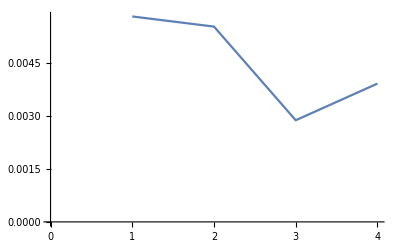

```mathematica
data=AbsoluteTiming[#/@z][[1]]&/@{f1,f2,f3,f4};ListLinePlot[data]
```

效率：符号符号，函数，纯函数，编译函数